```mathematica
SetDirectory[NotebookDirectory[]];
```

# Model 019

## Constants

```mathematica
G=Quantity["GravitationalConstant"];
ϵff=1/100;
κ=1;
αB=Quantity[259*10^-15,("Centimeters")^3* ("Seconds")^-1];
mp=Quantity["ProtonMass"];
σv=Quantity[6*10^-17,("Centimeters")^3*("Seconds")^-1];
Zsun=134/10000;
C₁=UnitConvert[κ/ϵff √((3*π)/(32*G)),"Gigayears"*("SolarMass")^(1/2)*("Parsecs")^(-3/2)];
C₂=UnitConvert[mp/αB,"Gigayears"*"SolarMass"*("Parsecs")^-3];
C₃=UnitConvert[(Zsun*mp)/(2*σv),"Gigayears"*"SolarMass"*("Parsecs")^-3];
```

```mathematica
c₁=QuantityMagnitude[C₁];(*[Gyr (M_(\[PermutationProduct]))^(1/2) pc^(-3/2)]*)
c₂=QuantityMagnitude[C₂];(*[Gyr M_(\[PermutationProduct]) pc^-3]*)
c₃=QuantityMagnitude[C₃];(*[Gyr M_(\[PermutationProduct]) pc^-3]*)
Zeff=10^-3*Zsun;
Zsn=9/100;
R=18/100;
```

## System of equations

```mathematica
(*
	Ionized gas fraction:        i(t) / ρ -> y[1]
	Atomic gas fraction:         a(t) / ρ -> y[2]
	Molecular gas fraction:      m(t) / ρ -> y[3]
	Metal fraction:              z(t) / ρ -> y[4]
	Stellar fraction:            s(t) / ρ -> y[5]	
	where ρ = i(t) + a(t) + m(t) + s(t)
     
	Each equation has Gyr^(-1) [years^(-9)] as its units on the LHS and RHS
*)
```

```mathematica
vars={i[t],a[t],m[t],z[t],s[t]};
g=i[t]+m[t]+a[t];
τS=(c₁*g0)/(√(g*ρ0)); 
τR=c₂/(i[t]*ρ0);
τC=c₃/(g*ρ0*(z[t]+Zeff));
recombination=i[t]/τR;
cloudFormation=a[t]/τC;
ψ=m[t]/τS;
equ= {
i'[t]==-recombination+(etaIon+R)*ψ,
a'[t]==-cloudFormation+recombination+(etaDiss-etaIon)*ψ,
m'[t]==cloudFormation-(1+etaDiss)*ψ,
z'[t]==(Zsn*R-z[t])*ψ,
s'[t]==(1-R)*ψ
};
```

## Solving the system

### Integration span

```mathematica
Tstart=0; (*[Gyr]*)
Tend=1; (*[Gyr]*)
```

### Initial conditions

```mathematica
i0=9/10;
a0=5/100;
m0=5/100;
z0=10^-4;
s0=0;
initCond={i0,a0,m0,z0,s0};
```

### Parameters

```mathematica
n=Quantity[9/10,("Centimeters")^-3];
params = Normal[AssociationThread[
{ρ0,g0,etaIon,etaDiss},
{QuantityMagnitude[UnitConvert[mp*n,"SolarMass"*("Parsecs")^-3]],i0+a0+m0,95529/100,38093/100}
]];
```

### Integration

```mathematica
system = Join[equ,
{
i[Tstart]==i0,
a[Tstart]==a0,
m[Tstart]==m0,
z[Tstart]==z0,
s[Tstart]==s0
}]/.params;
solutions=vars/.NDSolve[system,vars,{t,Tstart,Tend}][[1]];
```

### Save data in file

```mathematica
lf=Log10[Tend]; 
li=lf-5;
points=10^4;
step=5/points;
times=N[Table[10^i,{i,li,lf,step}],8];
```

```mathematica
denseData=Table[{N[t,6],solutions[[1]],solutions[[2]],solutions[[3]],solutions[[4]], solutions[[5]]},{t,times}];
output=Prepend[denseData,{"t    i(t)    a(t)    m(t)    z(t)    s(t)"}];
```

```mathematica
Export["plots/mathematica.dat",output,"Table"];
```

## Plots

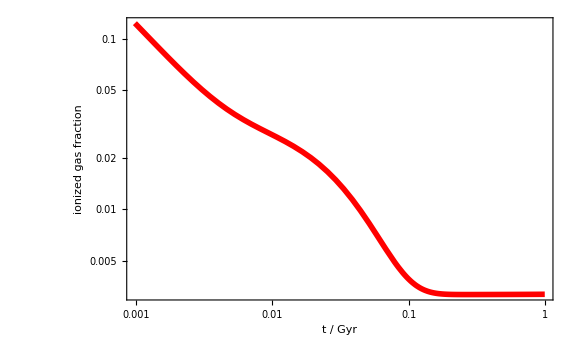

```mathematica
LogLogPlot[
solutions[[1]],{t,Tstart,Tend},
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["ionized gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

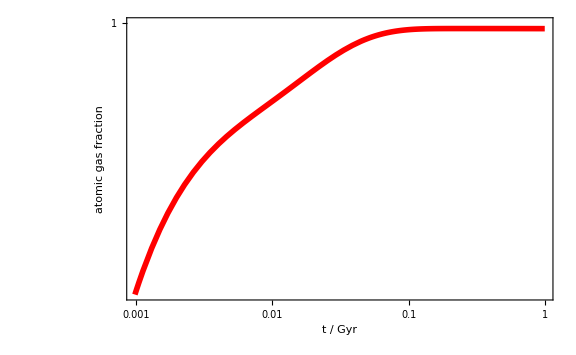

```mathematica
LogLogPlot[
solutions[[2]],{t,Tstart,Tend},
PlotStyle->{Thickness[0.007],Red},
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["atomic gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

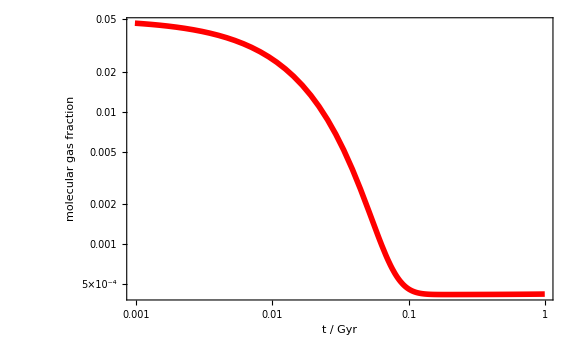

```mathematica
LogLogPlot[
solutions[[3]],{t,Tstart,Tend},
PlotStyle->{Thickness[0.007],Red},
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["molecular gas fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

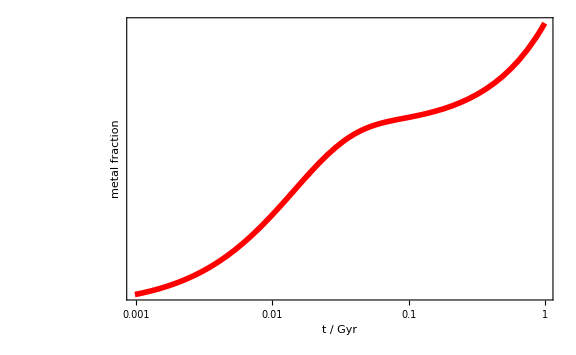

```mathematica
LogLogPlot[
solutions[[4]],{t,Tstart,Tend},
PlotStyle->{Thickness[0.007],Red},
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["metal fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

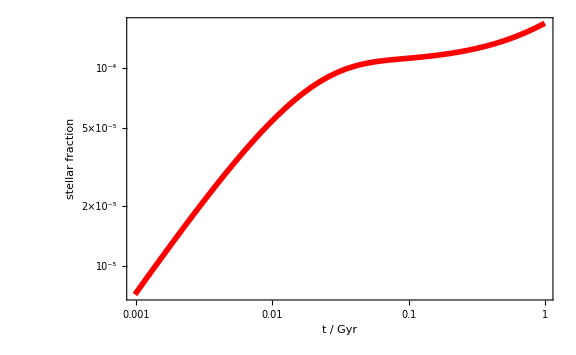

```mathematica
LogLogPlot[
solutions[[5]],{t,Tstart,Tend},
PlotStyle->{Thickness[0.007],Red},
PlotStyle->{Thickness[0.007],Red},
Frame->True,
FrameLabel->{Style["t / Gyr",16],Style["stellar fraction",16] },
FrameStyle->Directive[Black,14],
ImageSize->Large
]
```

## Jacobian matrix

### Jacobian evaluated at the initial condition

```mathematica
iniCondAss=Normal[AssociationThread[vars,initCond]];
jacobian=D[Map[(#[[2]])&,equ],{vars}]/.Join[iniCondAss,params];
ScientificForm[MatrixForm[N[jacobian,3]]]
```

(-1.32×10^4 | 4.40 | 1.80×10^2 | 0 | 0
1.32×10^4 | -2.68 | -1.08×10^2 | -1.27×10^1 | 0
-1.76 | -1.73 | -7.21×10^1 | 1.27×10^1 | 0
7.41×10^-5 | 7.41×10^-5 | 3.04×10^-3 | -9.21×10^-3 | 0
3.78×10^-3 | 3.78×10^-3 | 1.55×10^-1 | 0 | 0)

### Jacobian and time derivatives in C syntax

```mathematica
cStringAss=Join[
Normal[AssociationThread[
Map[ToString@*CForm,vars],
Table[ToString[y[i]],{i,0,Length[vars]-1}]
]],
{"Power(2.71828182845905,"->"exp(","Power"->"pow","Sqrt"->"sqrt","ρ"->"rho"}
];
```

```mathematica
CJacobian=Map[ToString@*CForm,N[FullSimplify[D[Map[(#[[2]])&,equ],{vars}]],10],{2}];
CJacobian=Map[StringReplace[#,cStringAss]&,CJacobian];
```

```mathematica
ExpTimeJacobian =ReplaceAll[Map[(#[[2]])&,equ],Normal[AssociationMap[Head,vars]]];
CTimeDeriv=Map[ToString@*CForm,N[D[ExpTimeJacobian,t],10]];
CTimeDeriv=Map[StringReplace[#,cStringAss]&,CTimeDeriv];
```

### Jacobian for Boost odeint

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\t\tJ(``,``) = ``;\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\t\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head="/*******************************************************************************************
* Jacobian for the model 019 calculated with Wolfram Language
* and adapted for its use with the Boost odeint library.
*******************************************************************************************/

struct jacobian
{
    template <class State, class Matrix>
    void operator()(const State &y, Matrix &J, const double &t, State &dfdt)
    {
        (void)(t);\n";
tail="    }
};";
Export["jacobian_boost.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

### Jacobian for GSL

```mathematica
jacobi=
StringJoin[
Flatten[
Table[
Join[{"\n"},
Table[
ToString[
StringForm["\tgsl_matrix_set(m, ``, ``, ``);\n",k-1,j-1,CJacobian[[k,j]]
]],{j,1,Length[vars]}]],{k,1,Length[vars]}]]];
timeDeriv=
Flatten[
Table[
ToString[
StringForm["\tdfdt[``] = ``;\n",j-1,CTimeDeriv[[j]]
]],{j,1,Length[vars]}]];
head=StringJoin["/*******************************************************************************************
* Jacobian for the model 019 calculated with Wolfram Language 
* and adapted for its use with the GSL library.
*******************************************************************************************/

int jacobian(double t, const double y[], double *dfdy, double dfdt[], void *params)
{
	(void)(t);

	struct Parameters *parameters = (struct Parameters *)params;

    double rho0 = parameters->rho0;
    double g0 = parameters->g0;
    struct InterpFunc *interp_ion = parameters->interp_ion;
    struct InterpFunc *interp_diss = parameters->interp_diss;

    double eta_ion = interp_eval(interp_ion, y[3]);
    double eta_diss = interp_eval(interp_diss, y[3]);\n\n",
ToString[
StringForm[
"\tgsl_matrix_view dfdy_mat = gsl_matrix_view_array(dfdy, ``, ``);\n",Length[vars],Length[vars]]],
	"\tgsl_matrix * m = &dfdy_mat.matrix;\n"];
tail="
	return GSL_SUCCESS;
};";
Export["jacobian_gsl.txt",StringJoin[head,jacobi,"\n",timeDeriv,tail]];
```

## Stiffness coefficient

```mathematica
StiffCoeff[equ_, vars_, y0_,params_]:=
Module[
{jacobian, association,Njacobian,eigenval},
jacobian=D[Map[(#[[2]])&,equ],{vars}];
association=Normal[AssociationThread[vars,y0]];
Njacobian=N[jacobian/.Join[association,params],16];
eigenval=DeleteCases[RealAbs[Re[Chop[Eigenvalues[Njacobian],10^-16]]],x_/;x==0];
Return[Max[eigenval]/Min[eigenval]];
]
```

```mathematica
StiffCoeff[equ,vars,initCond,params]
```

1.53×10^6